```mathematica
Integrate[I(π/h)^(3/2)(x+I y)^(1/2)Exp[- λ π/h(x+I y)]Exp[-I(π/h(x+I y)- ν π/2- π/4)],{y,-z,0}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0, m≥ 0,σ>0}]+Integrate[-I(π/h)^(3/2)(x+I y)^(1/2)Exp[- λ π/h(x+I y)]Exp[I(π/h(x+I y)- ν π/2- π/4)],{y,0,z}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0,m≥ 0}]-Integrate[-I(π/h)^(3/2)(x+I y)^(1/2)Exp[- λ π/h(x+I y)]Exp[I(π/h(x+I y)- ν π/2- π/4)],{y,z,0}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0,m≥ 0}]-Integrate[I(π/h)^(3/2)(x+I y)^(1/2)Exp[- λ π/h(x+I y)]Exp[-I(π/h(x+I y)- ν π/2- π/4)],{y,0,-z}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0, m≥ 0,σ>0}]
```

1/(2 √h (-ⅈ+λ)^(3/2))(-1)^(3/4) ⅇ^(-(π (z (2+2 ⅈ λ)+2 x (-ⅈ+λ)+ⅈ h ν))/(2 h)) √π (-2 (-ⅇ^((π z (1+ⅈ λ))/h) √x+√(x+ⅈ z)) √(-ⅈ+λ)+ⅇ^((π (x+ⅈ z) (-ⅈ+λ))/h) √h Erf[√π √((x+ⅈ z)/h) √(-ⅈ+λ)]-ⅇ^((π (x+ⅈ z) (-ⅈ+λ))/h) √h Erf[√π √((x (-ⅈ+λ))/h)])-1/(2 √h (-ⅈ+λ)^(3/2))(-1)^(3/4) ⅇ^(-(π (z (2+2 ⅈ λ)+2 x (-ⅈ+λ)+ⅈ h ν))/(2 h)) √π (2 (-ⅇ^((π z (1+ⅈ λ))/h) √x+√(x+ⅈ z)) √(-ⅈ+λ)-ⅇ^((π (x+ⅈ z) (-ⅈ+λ))/h) √h Erf[√π √((x+ⅈ z)/h) √(-ⅈ+λ)]+ⅇ^((π (x+ⅈ z) (-ⅈ+λ))/h) √h Erf[√π √((x (-ⅈ+λ))/h)])-1/(2 √h (ⅈ+λ)^(3/2))(-1)^(1/4) ⅇ^(-(π (2 z+2 x (ⅈ+λ)-ⅈ h ν))/(2 h)) √π (2 (ⅇ^((π z)/h) √x-ⅇ^((ⅈ π z λ)/h) √(x-ⅈ z)) √(ⅈ+λ)+ⅇ^((π (z+x (ⅈ+λ)))/h) √h Erf[√π √((x-ⅈ z)/h) √(ⅈ+λ)]-ⅇ^((π (z+x (ⅈ+λ)))/h) √h Erf[√π √((x (ⅈ+λ))/h)])+1/(2 √h (ⅈ+λ)^(3/2))(-1)^(1/4) ⅇ^(-(π (2 z+2 x (ⅈ+λ)-ⅈ h ν))/(2 h)) √π (2 (-ⅇ^((π z)/h) √x+ⅇ^((ⅈ π z λ)/h) √(x-ⅈ z)) √(ⅈ+λ)-ⅇ^((π (z+x (ⅈ+λ)))/h) √h Erf[√π √((x-ⅈ z)/h) √(ⅈ+λ)]+ⅇ^((π (z+x (ⅈ+λ)))/h) √h Erf[√π √((x (ⅈ+λ))/h)])

```mathematica
Simplify[Normal@Series[%11/.ν-> 0/.x-> h (n+1/4),{h,0,2}],Assumptions->{z>0,h>0,n>0,λ>0}]
```

ⅇ^(-(π (12 z+h (1+4 n) (ⅈ+3 λ)))/(4 h)) ((ⅇ^((π (z (4+2 ⅈ λ)+h (1+4 n) λ))/(2 h)) √π ((h+4 h n)^2+128 z^2+16 ⅈ h (z+4 n z)))/(64 √h z^(3/2) (ⅈ+λ))-(ⅈ ⅇ^((π (12 z+h (1+4 n) (ⅈ+3 λ)))/(4 h)) √(π-ⅈ π λ))/(ⅈ+λ)^2+(ⅈ ⅇ^((π (12 z+h (1+4 n) (ⅈ+3 λ)))/(4 h)) √(π+ⅈ π λ))/(-ⅈ+λ)^2+1/(64 √h π^(3/2) z^(3/2) (-ⅈ+λ)^3)ⅇ^((π (2 z (2-ⅈ λ)+h (1+4 n) (ⅈ+λ)))/(2 h)) (128 π^2 z^2 (-ⅈ+λ)^2-16 ⅈ h π z (-ⅈ+λ) (4+(1+4 n) π (-ⅈ+λ))+h^2 (32+8 (1+4 n) π (-ⅈ+λ)+(1+4 n)^2 π^2 (-ⅈ+λ)^2))+(ⅇ^((π (z (4+2 ⅈ λ)+h (1+4 n) λ))/(2 h)) √h (8 ⅈ π z (ⅈ+λ)+h (4+(1+4 n) π (ⅈ+λ))))/(8 π^(3/2) z^(3/2) (ⅈ+λ)^3)-1/((1+λ^2)^(3/2))ⅇ^((3 π z)/h+(π λ)/4+n π λ) √π (((1+ⅈ) ⅇ^((π λ)/4+n π λ) √((1+4 n) (1+λ^2)) (-ⅈ+λ+ⅇ^(2 ⅈ n π) (ⅈ+λ)))/(√2)+(-1)^(3/4) ⅇ^(1/4 (1+4 n) π (ⅈ+2 λ)) (ⅈ+λ)^(3/2) Erf[√π √((1/4+n) (-ⅈ+λ))]-(-1)^(1/4) ⅇ^(1/4 (1+4 n) π (ⅈ+2 λ)) (-ⅈ+λ)^(3/2) Erf[√π √((1/4+n) (ⅈ+λ))]))

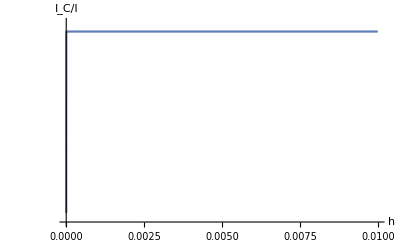

```mathematica
LogPlot[{Abs[1/(4 π I (λ/((1+λ^2)^(3/2))))%11/.z-> π/3/.x-> h(n+(π ν)/2+π/4)/.λ-> 0.1/.n-> 30/.ν-> 0]},{h,0,0.01},AxesLabel->{"h","I_C/I"}, PlotRange->All]
```

```mathematica
Integrate[Exp[- λ x]BesselJ[0, x] x,{x,0,Infinity}, Assumptions->{x>0,λ>0}]
```

λ/((1+λ^2)^(3/2))

```mathematica
Integrate[(π/h)^(3/2)(x+I y)^(1/2)Exp[- π^2/(4 h^2 σ^2)(x+I y)^2]Exp[I(π/h(x+I y)- ν π/2- π/4)],{y,0,z}, Assumptions->{h>0,z>0,x>0,σ>0}]
```

Integrate[ⅇ^(ⅈ (-π/4+(π (x+ⅈ y))/h-(π ν)/2)-(π^2 (x+ⅈ y)^2)/(4 h^2 σ^2)) (1/h)^(3/2) π^(3/2) √(x+ⅈ y),{y,0,z},Assumptions→{h>0,z>0,x>0,σ>0}]

```mathematica
Plot3D[Abs[%240/.x-> h(n+(π ν)/2+π/4)/.λ-> 1/.z-> π/2/.ν-> 0], {n,1,10},{h,0.001,0.1}]
```

-Graphics3D-

```mathematica
%240/.x-> h(n+(π ν)/2+π/4)/.λ-> 1/.z-> π/3/.ν-> 0
```

1/(2 (1-ⅈ)^(3/2) √h)(-1)^(3/4) ⅇ^(-(((2-2 ⅈ) h (n+π/4)+(2/3+(2 ⅈ)/3) π) π)/(2 h)) √π (-2 √(1-ⅈ) (√(h (n+π/4)+(ⅈ π)/3)-ⅇ^(((1/3+ⅈ/3) π^2)/h) √(h (n+π/4)))-ⅇ^(((1-ⅈ) (h (n+π/4)+(ⅈ π)/3) π)/h) √h Erf[√((1-ⅈ) (n+π/4)) √π]+ⅇ^(((1-ⅈ) (h (n+π/4)+(ⅈ π)/3) π)/h) √h Erf[√((h (n+π/4)+(ⅈ π)/3)/h) √((1-ⅈ) π)])+1/(2 (1+ⅈ)^(3/2) √h)(-1)^(1/4) ⅇ^(-(((2+2 ⅈ) h (n+π/4)+(2 π)/3) π)/(2 h)) √π (2 √(1+ⅈ) (ⅇ^((ⅈ π^2)/(3 h)) √(h (n+π/4)-(ⅈ π)/3)-ⅇ^(π^2/(3 h)) √(h (n+π/4)))+ⅇ^((((1+ⅈ) h (n+π/4)+π/3) π)/h) √h Erf[√((1+ⅈ) (n+π/4)) √π]-ⅇ^((((1+ⅈ) h (n+π/4)+π/3) π)/h) √h Erf[√((h (n+π/4)-(ⅈ π)/3)/h) √((1+ⅈ) π)])

```mathematica
Simplify[Integrate[x^(1/2)Cos[x]Exp[- λ x],{x,R,Infinity}, Assumptions->{R>0,λ>0}], Assumptions->{λ>0,R>0}]/(λ/((1+λ^2)^(3/2)))//Expand
```

(ⅇ^(-2 R λ+R (-ⅈ+λ)) √R √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))+(ⅇ^(2 ⅈ R-2 R λ+R (-ⅈ+λ)) √R √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))-(ⅈ ⅇ^(-2 R λ+R (-ⅈ+λ)) √R √(1+λ^2))/(2 λ (-ⅈ+λ) (ⅈ+λ))+(ⅈ ⅇ^(2 ⅈ R-2 R λ+R (-ⅈ+λ)) √R √(1+λ^2))/(2 λ (-ⅈ+λ) (ⅈ+λ))-(ⅈ ⅇ^(-2 R λ+R (-ⅈ+λ)) √R λ √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))+(ⅈ ⅇ^(2 ⅈ R-2 R λ+R (-ⅈ+λ)) √R λ √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))+(ⅇ^(-2 R λ+R (-ⅈ+λ)) √R λ^2 √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))+(ⅇ^(2 ⅈ R-2 R λ+R (-ⅈ+λ)) √R λ^2 √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))+(ⅇ^(-2 R λ+R (-ⅈ+λ)+R (ⅈ+λ)) √π (1+λ^2)^(3/4) Cos[3/2 ArcTan[1/λ]])/(2 λ (-ⅈ+λ) (ⅈ+λ))+(ⅇ^(-2 R λ+R (-ⅈ+λ)+R (ⅈ+λ)) √π λ (1+λ^2)^(3/4) Cos[3/2 ArcTan[1/λ]])/(2 (-ⅈ+λ) (ⅈ+λ))-(√π √(1+λ^2) Erf[√(R (-ⅈ+λ))])/(4 (-ⅈ+λ)^(3/2) (ⅈ+λ))-(ⅈ √π √(1+λ^2) Erf[√(R (-ⅈ+λ))])/(4 λ (-ⅈ+λ)^(3/2) (ⅈ+λ))-(ⅈ √π λ √(1+λ^2) Erf[√(R (-ⅈ+λ))])/(4 (-ⅈ+λ)^(3/2) (ⅈ+λ))-(√π λ^2 √(1+λ^2) Erf[√(R (-ⅈ+λ))])/(4 (-ⅈ+λ)^(3/2) (ⅈ+λ))+(ⅈ √π Erf[√(R (ⅈ+λ))])/(2 (-ⅈ+λ)^(3/2) (ⅈ+λ))+(√π Erf[√(R (ⅈ+λ))])/(4 λ (-ⅈ+λ)^(3/2) (ⅈ+λ))+(ⅈ √π λ^2 Erf[√(R (ⅈ+λ))])/(2 (-ⅈ+λ)^(3/2) (ⅈ+λ))-(√π λ^3 Erf[√(R (ⅈ+λ))])/(4 (-ⅈ+λ)^(3/2) (ⅈ+λ))

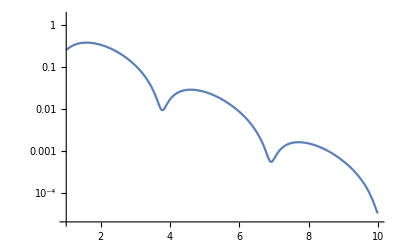

```mathematica
LogPlot[Abs[(ⅇ^(-2 R λ+R (-ⅈ+λ)) √R √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))+(ⅇ^(2 ⅈ R-2 R λ+R (-ⅈ+λ)) √R √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))-(ⅈ ⅇ^(-2 R λ+R (-ⅈ+λ)) √R √(1+λ^2))/(2 λ (-ⅈ+λ) (ⅈ+λ))+(ⅈ ⅇ^(2 ⅈ R-2 R λ+R (-ⅈ+λ)) √R √(1+λ^2))/(2 λ (-ⅈ+λ) (ⅈ+λ))-(ⅈ ⅇ^(-2 R λ+R (-ⅈ+λ)) √R λ √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))+(ⅈ ⅇ^(2 ⅈ R-2 R λ+R (-ⅈ+λ)) √R λ √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))+(ⅇ^(-2 R λ+R (-ⅈ+λ)) √R λ^2 √(1+λ^2))/(2 (-ⅈ+λ) (ⅈ+λ))]/.λ-> 1,{R,1,10}]
```

```mathematica
Simplify[Integrate[x BesselJ[0,x]Exp[- λ x],{x,0,Infinity}, Assumptions->{R>0,λ>0}], Assumptions->{λ>0,R>0}]//Expand
```

λ/((1+λ^2)^(3/2))

```mathematica
D[λ/((1+λ^2)^(3/2)), λ]
```

-(3 λ^2)/((1+λ^2)^(5/2))+1/((1+λ^2)^(3/2))

```mathematica
∫(-(3 λ^2)/((1+λ^2)^(5/2))+1/((1+λ^2)^(3/2)))ⅆλ
```

λ/((1+λ^2)^(3/2))

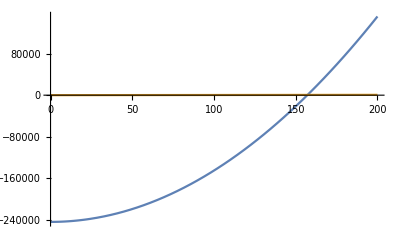

```mathematica
Plot[{π^2/0.01^2((0.01x)^2-(π/2)^2),π x},{x,0,200}]
```